```mathematica
?Table
```

Table[expr,n] generates a list of n copies of expr. 
Table[expr,{i,i_max}] generates a list of the values of expr when i runs from 1 to i_max. 
Table[expr,{i,i_min,i_max}] starts with i=i_min. 
Table[expr,{i,i_min,i_max,di}] uses steps di. 
Table[expr,{i,{i_1,i_2,…}}] uses the successive values i_1, i_2, ….
Table[expr,{i,i_min,i_max},{j,j_min,j_max},…] gives a nested list. The list associated with i is outermost.

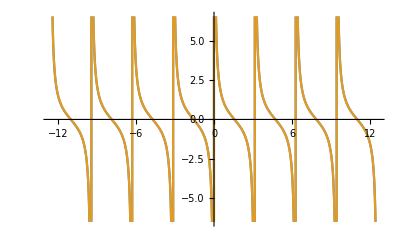

```mathematica
Plot[{ratCotApprox[100],Cot[x]},{x,-4π,4π}]
```

```mathematica
ratCotApprox[n_]:=Fold[Plus,Table[1/(x+k π),{k,-n,n}]]
```

```mathematica
sumOfLnsLnSinApprox[n_]:=Fold[Plus,Table[Log[Abs[k π+x]],{k,-n,n-1}]]
```

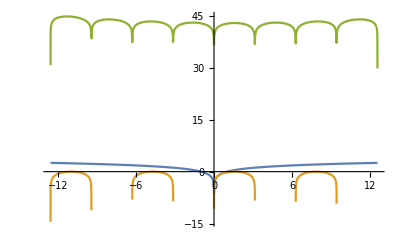

```mathematica
Plot[{Log[Abs[x]],Log[Sin[x]],sumOfLnsLnSinApprox[9]},{x,-4π,4π}]
```

```mathematica
2,4,8,13,18,24,30,36
```

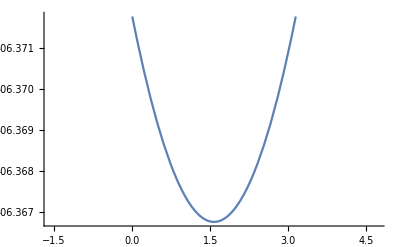

```mathematica
Plot[sumOfLnsLnSinApprox[50]-Log[Sin[x]],{x,-π/2,3π/2}]
```

```mathematica
a[n_]:=((-1)^n 2^(2n-1)(2^(2n)-1)BernoulliB[2n])/(n Factorial[2n])
```

```mathematica
a[4]
```

-17/2520

```mathematica
seriesApproxLnCos[n_]:=Fold[Plus,Table[a[k] x^(2k),{k,1,n}]]
```

```mathematica
seriesApproxLnCos[7]
```

x^2/2+x^4/12+x^6/45+(17 x^8)/2520+(31 x^10)/14175+(691 x^12)/935550+(10922 x^14)/42567525

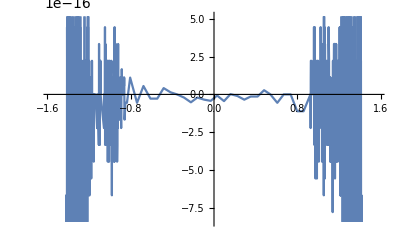

```mathematica
Plot[{Log[Cos[x]]-seriesApproxLnCos[150]},{x,-π/2,π/2}]
```

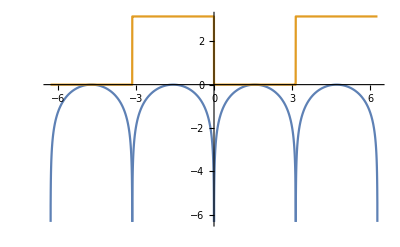

```mathematica
Plot[{Re[Log[Sin[z]]], Im[Log[Sin[z]]]},{z,-2π,2π}]
```

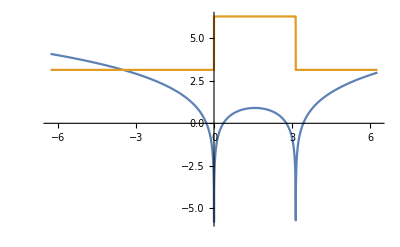

```mathematica
Plot[{Re[Log[x-π]]+Re[Log[-x]],Im[Log[x-π]]+Im[Log[-x]]},{x,-2π,2π}]
```

```mathematica
Integrate[1/x,x]
```

Log[x]

```mathematica
?Integrate
```

Integrate[f,x] gives the indefinite integral ∫f dx. 
Integrate[f,{x,x_min,x_max}] gives the definite integral ∫_x_min^x_max f dx. 
Integrate[f,{x,x_min,x_max},{y,y_min,y_max},…] gives the multiple integral ∫_x_min^x_max dx∫_y_min^y_max dy … f. 
Integrate[f,{x,y,…}∈reg] integrates over the geometric region reg.

```mathematica
D[Log[x],x]
```

1/x

```mathematica
?RandomReal
```

RandomReal[] gives a pseudorandom real number in the range 0 to 1. 
RandomReal[{x_min,x_max}] gives a pseudorandom real number in the range x_min to x_max. 
RandomReal[x_max] gives a pseudorandom real number in the range 0 to x_max.
RandomReal[range,n] gives a list of n pseudorandom reals. 
RandomReal[range,{n_1,n_2,…}] gives an n_1×n_2×… array of pseudorandom reals.

```mathematica
RandomReal[{0,π}]
```

2.81227

```mathematica
f[pair_]:=(pair[[1]]-pair[[2]])/2
```

```mathematica
Min[Map[f,Table[{RandomReal[{-π,π}],RandomReal[{-π,π}]},10000]]]
```

-3.02728

Map[f,expr] or f/@expr applies f to each element on the first level in expr. 
Map[f,expr,levelspec] applies f to parts of expr specified by levelspec. 
Map[f] represents an operator form of Map that can be applied to an expression.

```mathematica
{1,4,3}[[2]]
```

4

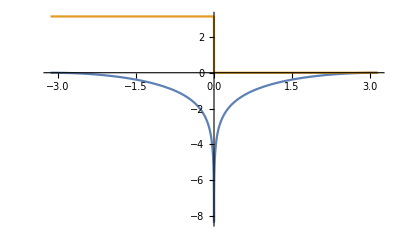

```mathematica
Plot[{Re[Log[Sin[x/2]]],Im[Log[Sin[x/2]]]},{x,-π,π}]
```

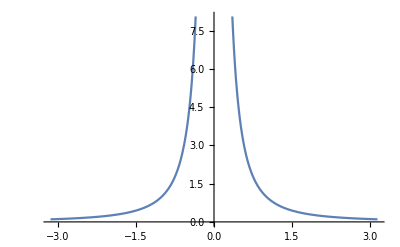

```mathematica
Plot[1/x^2,{x,-π,π}]
```

```mathematica
Table[Fold[Plus,Table[With[{a=N[Integrate[Log[Abs[x]]/x^(1/k),{x,0,π}]]},a/x^(1/k)],{k,2,n}]],{n,2,6}]
```

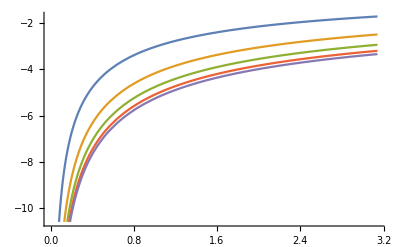

```mathematica
Plot[{-3.031853614781262/(√x),-3.031853614781262/(√x)-1.1430972581520396/x^(1/3),-3.031853614781262/(√x)-1.1430972581520396/x^(1/3)-0.5934044080031612/x^(1/4),-3.031853614781262/(√x)-1.1430972581520396/x^(1/3)-0.5934044080031612/x^(1/4)-0.3288024197909893/x^(1/5),-3.031853614781262/(√x)-1.1430972581520396/x^(1/3)-0.5934044080031612/x^(1/4)-0.3288024197909893/x^(1/5)-0.1721722552207652/x^(1/6)},{x,0,π}]
```

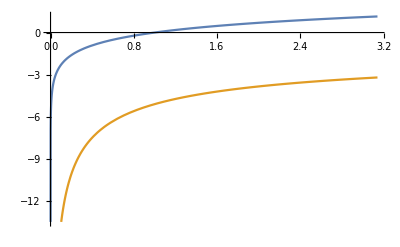

```mathematica
Plot[{Log[x],-3.031853614781262/(√x)-1.1430972581520396/x^(1/3)-0.5934044080031612/x^(1/4)-0.3288024197909893/x^(1/5)},{x,0,π}]
```

```mathematica
Fold[Plus,{((2-2 ⅈ) √π (-2+Log[π]))/(√x),-(3 (-3 (-π)^(2/3)+3 π^(2/3)+2 (-π)^(2/3) Log[π]-2 π^(2/3) Log[π]))/(4 x^(1/3)),-(4 (-4 (-π)^(3/4)+4 π^(3/4)+3 (-π)^(3/4) Log[π]-3 π^(3/4) Log[π]))/(9 x^(1/4)),-(5 (-5 (-π)^(4/5)+5 π^(4/5)+4 (-π)^(4/5) Log[π]-4 π^(4/5) Log[π]))/(16 x^(1/5))}]
```

```mathematica
Plot[((2-2 ⅈ) √π (-2+Log[π]))/(√x)-(3 (-3 (-π)^(2/3)+3 π^(2/3)+2 (-π)^(2/3) Log[π]-2 π^(2/3) Log[π]))/(4 x^(1/3))-(4 (-4 (-π)^(3/4)+4 π^(3/4)+3 (-π)^(3/4) Log[π]-3 π^(3/4) Log[π]))/(9 x^(1/4))-(5 (-5 (-π)^(4/5)+5 π^(4/5)+4 (-π)^(4/5) Log[π]-4 π^(4/5) Log[π]))/(16 x^(1/5)),{x,-π,π}]
```

-Graphics-

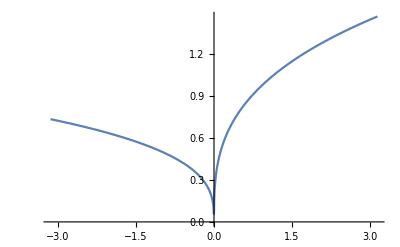

```mathematica
Plot[Re[x^(1/3)],{x,-π,π}]
```